# QG Inertial modes in a sphere

This script codes the formulas of Zhang et al., 2001 (“On inertial waves in a rotating fluid sphere”) and calculates equatorially symmetric inertial normal modes. This code has been uploaded as supplementary material to Maffei, Jackson and Livermore “Characterisation of columnar inertial modes in rapidly rotating spheres and spheroids” (PRSA) and has been used to generate the QGIW solutions of figures 3 and 4. It can, however be used to visualize general 3D solutions in a sphere.

Usage: Evaluate the notebook and change the parameters m1, n1, i1, to view different modes.

## Equatorially symmetric modes

### Find the frequencies

```mathematica
W[NG_,m_]:=Sum[(  (-1)^j Factorial[2(2 NG + m - j)]/(Factorial[j]Factorial[2 NG+m-j]Factorial[2(NG-j)]) ) ( (m+2 NG - 2 j) - 2(NG-j)/σ  ) σ^(2(NG-j)),{j,0,NG}]
```

```mathematica
sigma[m_,NG_]:=σ/. Solve[W[NG,m]==0,σ]
```

```mathematica
N[sigma[3, 2], 18]*2
```

{-1.0221792004706045,-0.120346611831856556,0.773459954263417633,1.51192300089618628}

### Calculate velocity field

```mathematica
C3D[i_,j_,m_,NG_]:=(-1)^(i+j)(2(m+NG+i+j)-1.)!!/(2^(j+1)(2i-1)!!(NG-i-j)!i!j!(m+j)!)
```

```mathematica
Us3D[s_,z_,m_,NG_,n_]:=-ⅈ Sum[  C3D[i,j,m,NG]( sigma[m,NG][[n]])^(2i)(1-( sigma[m,NG][[n]])^2)^(j-1)(m+m ( sigma[m,NG][[n]])+2j ( sigma[m,NG][[n]]))s^(m+2j-1)z^(2i),{i,0,NG},{j,0,NG-i}] // Simplify
```

```mathematica
Uz3D[s_,z_,m_,NG_,n_]:=ⅈ Sum[C3D[i,j,m,NG]( sigma[m,NG][[n]])^(2i-1) (1-( sigma[m,NG][[n]])^2)^j (2i )s^(m+2j)z^(2i-1),{i,0,NG},{j,0,NG-i}]
```

```mathematica
Uphi3D[s_,z_,m_,NG_,n_]:=Sum[C3D[i,j,m,NG]( sigma[m,NG][[n]])^(2i)(1-( sigma[m,NG][[n]])^2)^(j-1)(m+m ( sigma[m,NG][[n]]) + 2j) s^(m+2j-1) z^(2i) ,{i,0,NG},{j,0,NG-i}]
```

## Visualisation & post-processing

The quasi-geostrophic modes are reproduced when n1=N1, when the lowermost eigenfrequency is selected

```mathematica
m1=3;
n1=1;
N1=2;
sigma[m1,N1]//N

U3D={Us3D[s,z,m1,N1,n1],Uphi3D[s,z,m1,N1,n1],Uz3D[s,z,m1,N1,n1]}Exp[ⅈ m1 phi];
U3DS=TransformedField["Cylindrical"->"Spherical",U3D,{s,phi,z}->{R,Th,Ph}];
```

{-0.51109,-0.0601733,0.38673,0.755962}

```mathematica
phiView = (1/15) Pi
```

π/15

σ = -0.51109

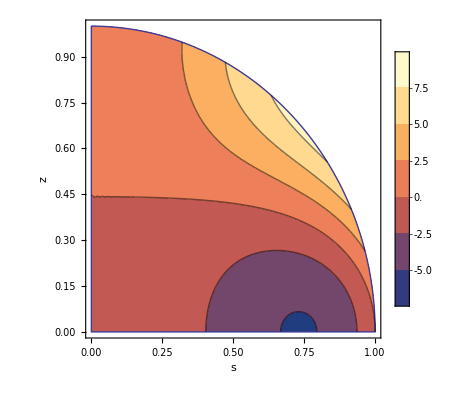
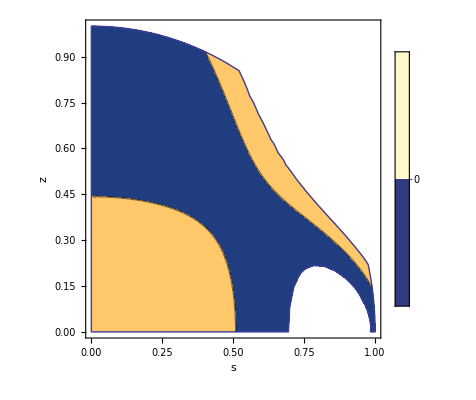
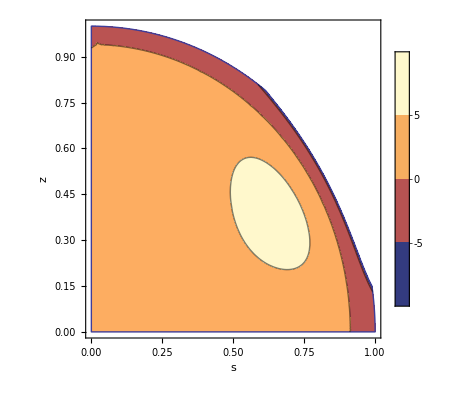
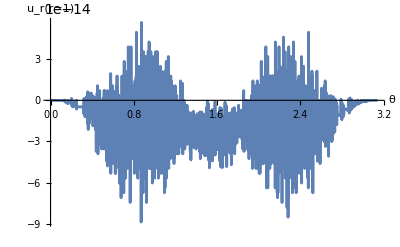

```mathematica
str="σ = " <>ToString[sigma[m1,N1][[n1]]//N]
plots1=Table[ContourPlot[Im[U3D[[i]]]+Re[U3D[[i]]]/. phi->phiView,{s,0,1},{z,0,1},RegionFunction->Function[{s,z},s^2+z^2≤1],FrameLabel->{"s","z"},BoundaryStyle->Automatic,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->10}]],{i,1,3}];
plot2=Plot[Im[U3DS[[1]]]+Re[U3DS[[1]]]/.R->1/.Ph->0,{Th,0,Pi},AxesLabel->{"θ","u_r(r=1)"}];
Join[plots1,{plot2}]
```

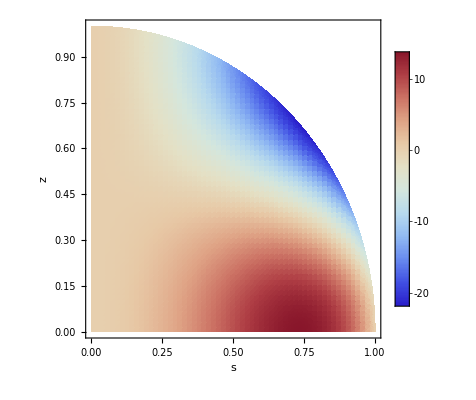
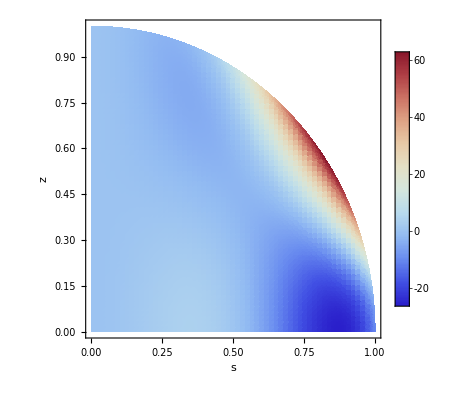
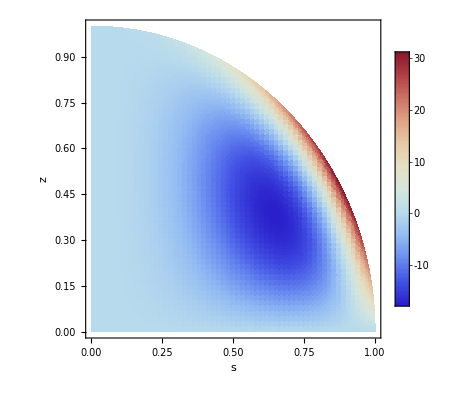

```mathematica
azmView = Pi/15;
plotsRe=Table[DensityPlot[Re[U3D[[i]] /. phi->phiView],{s,0,1},{z,0,1},RegionFunction->Function[{s,z},s^2+z^2≤1],FrameLabel->{"s","z"},PlotRange->All, PlotPoints->60,ColorFunction->"ThermometerColors",PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->10}]],{i,1,3}]
```

### Malkus frequencies

### Generate the figures for u_s as they appear on Maffei, Jackson and Livermore (Characterisation of columnar inertial modes in rapidly rotating spheres and spheroids)

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::munfl: -9.83044×10^-33 7.74091870307026×10^-1365 is too small to represent as a normalized machine number; precision may be lost.

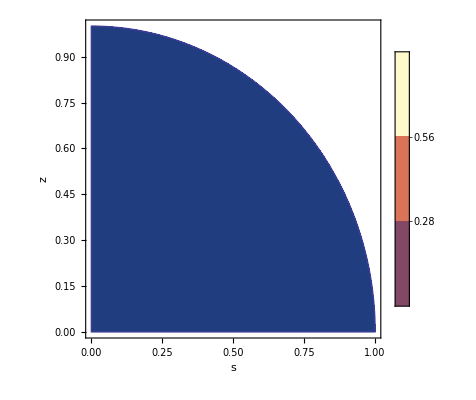

```mathematica
NFs=FindMaximum[ⅈ U3D[[1]],{s,z}][[1]];
ContourPlot[(Im[U3D[[1]]]+Re[U3D[[1]]])/NFs,{s,0,1},{z,0,1},RegionFunction->Function[{s,z},s^2+z^2≤1],FrameLabel->{"s","z"},BoundaryStyle->Automatic,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->20}],TicksStyle->Large,AxesStyle->Thick,LabelStyle->Large,Contours->6,PlotRange->Full]
```

## Equatorially anti-symmetric modes

### Find the frequencies

```mathematica
WA[NG_,m_]:=Sum[(  (-1)^j Factorial[2(2 NG + m - j + 1)]/(Factorial[j]Factorial[2 NG+m-j+1]Factorial[2(NG-j)+1]) ) ( (2 NG - 2 j + m + 1)σ  - (2(NG-j)+1) ) σ^(2(NG-j)),{j,0,NG}]
```

```mathematica
sigmaA[m_,NG_]:=σ/. Solve[WA[NG,m]==0,σ]
```

```mathematica
N[sigmaA[1,0], 18]*2
```

{1.}

### Calculate velocity field

```mathematica
C3DA[i_,j_,m_,NG_]:=(-1)^(i+j)(2(m+NG+i+j)+1.)!!/(2^(j+1)(2i+1)!!(NG-i-j)!i!j!(m+j)!)
```

```mathematica
Us3DA[s_,z_,m_,NG_,n_]:=-ⅈ Sum[  C3DA[i,j,m,NG]( sigmaA[m,NG][[n]])^(2i)(1-( sigmaA[m,NG][[n]])^2)^(j-1)(m+m ( sigmaA[m,NG][[n]])+2j ( sigmaA[m,NG][[n]]))s^(m+2j-1)z^(2i+1),{i,0,NG},{j,0,NG-i}] // Simplify
```

```mathematica
Uz3DA[s_,z_,m_,NG_,n_]:=ⅈ Sum[C3DA[i,j,m,NG]( sigmaA[m,NG][[n]])^(2i-1) (1-( sigmaA[m,NG][[n]])^2)^j (2i + 1 )s^(m+2j)z^(2i),{i,0,NG},{j,0,NG-i}]
```

```mathematica
Uphi3DA[s_,z_,m_,NG_,n_]:=Sum[C3DA[i,j,m,NG]( sigmaA[m,NG][[n]])^(2i)(1-( sigmaA[m,NG][[n]])^2)^(j-1)(m+m ( sigmaA[m,NG][[n]]) + 2j) s^(m+2j-1) z^(2i+1) ,{i,0,NG},{j,0,NG-i}]
```

## Visualisation & post-processing

Spin-over mode

```mathematica
m1=1;
n1=1;
N1=0;
sigmaA[m1,N1]//N

U3DA={Us3DA[s,z,m1,N1,n1],Uphi3DA[s,z,m1,N1,n1],Uz3DA[s,z,m1,N1,n1]} Exp[ⅈ m1 phi];
U3DSA=TransformedField["Cylindrical"->"Spherical",U3DA ,{s,phi,z}->{R,Th,Ph}];
```

{0.5}

```mathematica
phiView = (1/15) Pi
```

π/15

σ = 0.5

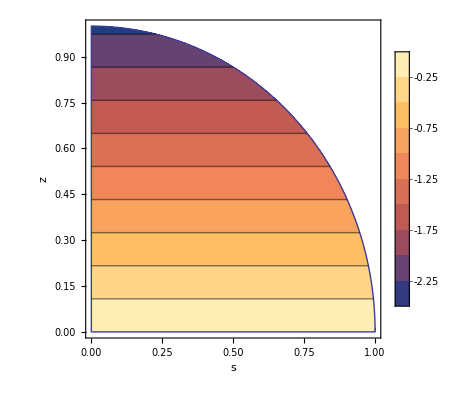
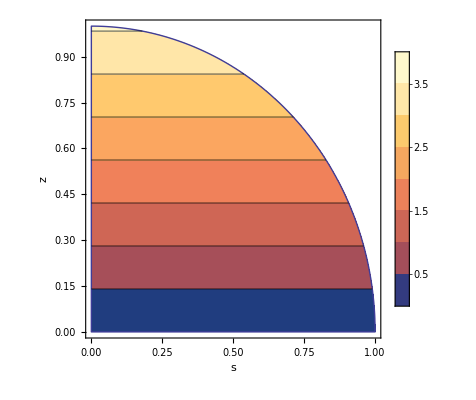
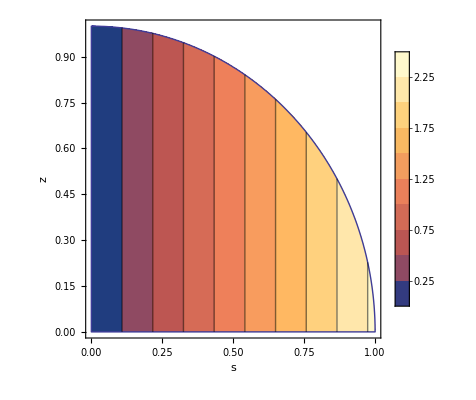
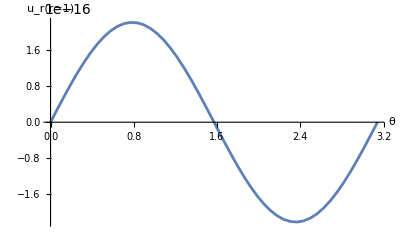

```mathematica
str="σ = " <>ToString[sigmaA[m1,N1][[n1]]//N]
plots1=Table[ContourPlot[Im[U3DA[[i]]]+Re[U3DA[[i]]] /. phi-> phiView,{s,0,1},{z,0,1},RegionFunction->Function[{s,z},s^2+z^2≤1],FrameLabel->{"s","z"},BoundaryStyle->Automatic,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->10}]],{i,1,3}];
plot2=Plot[Im[U3DSA[[1]]]+Re[U3DSA[[1]]]/.R->1/.Ph->0,{Th,0,Pi},AxesLabel->{"θ","u_r(r=1)"}];
Join[plots1,{plot2}]
```

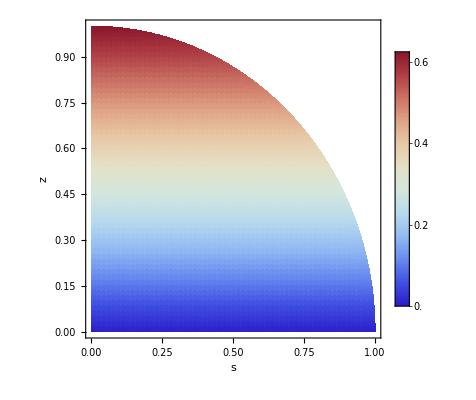
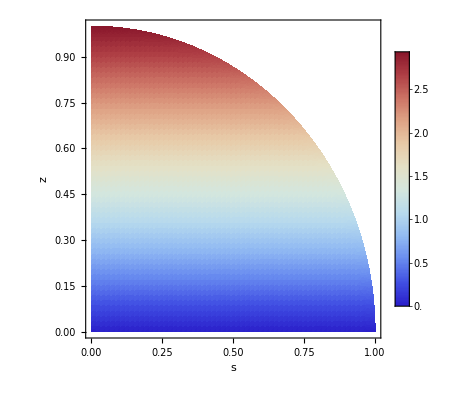
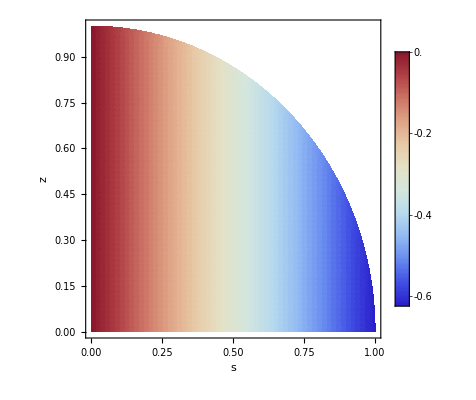

```mathematica
plots=Table[DensityPlot[Re[U3DA[[i]]]/.phi->phiView ,{s,0,1},{z,0,1},RegionFunction->Function[{s,z},s^2+z^2≤1],FrameLabel->{"s","z"},PlotRange->All, PlotPoints->60,ColorFunction->"ThermometerColors",PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->10}]],{i,1,3}]
```